```mathematica
Needs["Combinatorica`"]
Cseries[nSer_]:=Module[{i,j,p0,p,ρ,n,s,counts,key,val,delPart,orbit,dimO,dimM,dt,Γ1,Γ2,Γs,HS,HWG,mHL,CseriesModuli,Labels,CseriesModuliTable},
n=2nSer;
CseriesModuli={};
p0= IntegerPartitions[n];
(*delete some partitions*)
p={};
For[i=1,i≤Length[p0],i++,
counts=Counts[p0⟦i⟧];
key=Keys[counts];
val=Values[counts];
delPart=Or@@Table[OddQ[key⟦j⟧]&&OddQ[val⟦j⟧],{j,1,Length[key]}];
If[Not[delPart],AppendTo[p,p0⟦i⟧]]
];
ρ=Table[TransposePartition[p⟦i⟧],{i,1,Length[p]}];
s=Table[Table[0,{Length[TransposePartition[p⟦i⟧]]}],{i,1,Length[p]}];
For[i=1,i≤ Length[p], i++,
(*Orbit*)
counts=Counts[p⟦i⟧];
key=Keys[counts];
val=Values[counts];
orbit=Table[If[val⟦k⟧==1,key⟦k⟧,Superscript[key⟦k⟧,val⟦k⟧]],{k,1,Length[key]}];
(*dim(O)*)
(*dimO=(n(n+1))/2-(∑_(j=1)^Length[ρ⟦i⟧] ((ρ⟦i,j⟧(ρ⟦i,j⟧+1))Mod[j,2]))/2-(∑_(j=2)^Length[ρ⟦i⟧] ((ρ⟦i,j⟧(ρ⟦i,j⟧-1))Mod[j,2]))/2;*)
dimO=n(n+1)/2-Sum[ρ⟦i,j⟧(ρ⟦i,j⟧+1),{j,1,Length[ρ⟦i⟧],2}]/2-Sum[ρ⟦i,j⟧(ρ⟦i,j⟧-1),{j,2,Length[ρ⟦i⟧],2}]/2;

(*dim(M_H)*)
dimM=dimO/2;
(*string d^t*)
counts=Counts[ρ⟦i⟧];
key=Keys[counts];
val=Values[counts];
dt=Table[If[val⟦k⟧==1,key⟦k⟧,Superscript[key⟦k⟧,val⟦k⟧]],{k,1,Length[key]}];
(*Γ1*)
dx =2.5;
r=1;
For[j=1,j≤ Length[s⟦i⟧], j++,
If[j==1,s⟦i,j⟧=n-ρ⟦i,j⟧,s⟦i,j⟧=s⟦i,j-1⟧-ρ⟦i,j⟧];
];
Γ1=Graphics[{
{EdgeForm[{Thin,Blue}],White,Rectangle[{dx-r,dx+r+0.5},{dx+r,r+0.5}]},
If[i< Length [p],Line[{{dx,dx-3/2 r},{dx,dx-r}}]],
{Darker[Yellow],Table[Circle[{(k-1) dx,0},r],{k,3,Length[s[[i]]],2}]},
{Darker[Green],Table[Circle[{(k-1) dx,0},r],{k,2,Length[s[[i]]],2}]},
Table[Line[{{(k-2) dx+r,0},{(k-1) dx-r,0}}],{k,3,Length[s⟦i⟧]}],
Table[Text[s⟦i,k-1⟧,{(k-1) dx,0}],{k,2,Length[s[[i]]]}],
Text[n,{dx,dx+r/2}]
},ImageSize->{15n,40}];
(*Want to define from Hanany Kalveks patterns, need to implement that*)
γ = Table[1 ,nSer];
ϕ = 1;
ν=0;
σ =2;
(*Minimal*)
If [dimO ==(2nSer ), {ν =1,For[j = 2, j < Length[γ],j++,γ⟦j⟧= 1];}];
(*SupraMinimal*)
If [dimO ==(4nSer -2), {ϕ=1,ν = 2,For[j = 2, j ≤ Length[γ],j++,γ⟦j⟧= 2];}];

If[ ν > 0,
Γ2=Graphics[{
Line[{{σ  ν dx,0},{σ ν dx,σ r}}],

If[nSer >1,{Line[{{Abs[1-nSer]σ dx  ,0.3},{nSer σ dx  ,0.3}}]}],
If[nSer >1,{Line[{{Abs[1-nSer]σ dx  ,-0.3},{nSer σ dx  ,-0.3}}]}],

Line[{{σ nSer dx-σ,0},{σ nSer dx+r-σ,r}}],
Line[{{σ nSer dx-σ,0},{σ nSer dx+r-σ,-r}}],

Table[Line[{{k σ dx+r,0},{(k+1)σ dx-r,0}}],{k,nSer-2}],
{Blue,Table[Disk[{σ k dx,0},r],{k,1,nSer}]},

Table[Style[Text[γ⟦k⟧,{σ k dx,0}],White],{k,nSer}],

{Red,Rectangle[{σ ν dx-r,dx+r},{ν σ dx+r, r+0.5}]},
{Style[Text[ϕ,{σ ν dx,dx+r/(2 σ)}],White]}
},ImageSize->{15n,40}];
,Γ2="..."];
ι =φ =1;
If[OddQ[nSer],{ι = 1,φ =2},{ι = 2,φ =1}];
Γs =Graphics[{
{Black, Line[{{(σ dx) ,0},{((n) σ dx),0}}]},
{Darker[Green],Table[Disk[{σ k dx,0},r],{k,ι,n,2}]},
{Darker[Yellow],Table[Disk[{σ k dx,0},r],{k,φ,n,2}]}
}];
(*Hilbert Series for all C Series moduli spaces*)
If[ i==1, HS=(∏_(i=1)^nSer (1-t^(4i)))/((1-t^2)^(nSer(2nSer+1)))];
If [i>=2 ,HS=("polynom")/((1-t^2)^dimO)];
If [i==Length[p] ,HS=1];
(*Character HWG definition*)
If[i<Length[p]-3,HWG="..."];

If[i==Length[p], HWG=1];

If[ Length[s⟦i⟧]==2, HWG=1/(∏_(l=1)^s⟦i,1⟧ (1-Subscript[m, l]^2 t^(2l))) ];

(*modified Hall-Littelwood HWG function definition*)
If[i==1, mHL=1];
If[i==2,mHL=1-Subscript[h, 2] t^(4nSer-4)];
If[i>2,mHL="..."];
AppendTo[CseriesModuli,{orbit,dimO,dimM,dt,Γ1,Γ2,Γs,HS,HWG,mHL}]
];
CseriesModuli=Sort[CseriesModuli,#1[[2]]<#2[[2]]&];(*sort by dimO*)
Labels={{"Orbit","dim(O)","dim(ℳ_H)^ℍ","d^t","Γ_1","Γ_2^R","Γ_2^S","Higgs HS","Character HWG","mHL HWG"}};
CseriesModuliTable=Join[Labels,CseriesModuli];
Labeled[Grid[CseriesModuliTable,Frame->All,Background->{None,{LightGreen}},ItemSize->{Automatic,2},Alignment->Left],"Moduli Space Quivers for Nilpotent Orbits of "<>ToString[Subscript["C",nSer],TraditionalForm],Top]
]
```

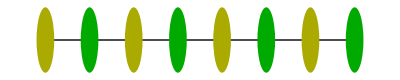
Orbit | dim(O) | dim(ℳ_H)^ℍ | d^t | Γ_1 | Γ_2^R | Γ_2^S | Higgs HS | Character HWG | mHL HWG
{1^8} | 0 | 0 | {8} | -Graphics- | ... | -Graphics- | 1 | 1 | ...
{2,1^6} | 8 | 4 | {7,1} | -Graphics- | -Graphics- | -Graphics- | polynom/((1-t^2)^8) | 1/(1-t^2 m_1^2) | ...
{2^2,1^4} | 14 | 7 | {6,2} | -Graphics- | -Graphics- | -Graphics- | polynom/((1-t^2)^14) | 1/((1-t^2 m_1^2) (1-t^4 m_2^2)) | ...
{2^3,1^2} | 18 | 9 | {5,3} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^18) | 1/((1-t^2 m_1^2) (1-t^4 m_2^2) (1-t^6 m_3^2)) | ...
{2^4} | 20 | 10 | {4^2} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^20) | 1/((1-t^2 m_1^2) (1-t^4 m_2^2) (1-t^6 m_3^2) (1-t^8 m_4^2)) | ...
{4,1^4} | 20 | 10 | {5,1^3} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^20) | ... | ...
{3^2,1^2} | 22 | 11 | {4,2^2} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^22) | ... | ...
{3^2,2} | 24 | 12 | {3^2,2} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^24) | ... | ...
{4,2,1^2} | 24 | 12 | {4,2,1^2} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^24) | ... | ...
{4,2^2} | 26 | 13 | {3^2,1^2} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^26) | ... | ...
{4^2} | 28 | 14 | {2^4} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^28) | ... | ...
{6,1^2} | 28 | 14 | {3,1^5} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^28) | ... | ...
{6,2} | 30 | 15 | {2^2,1^4} | -Graphics- | ... | -Graphics- | polynom/((1-t^2)^30) | ... | 1-t^12 h_2
{8} | 32 | 16 | {1^8} | -Graphics- | ... | -Graphics- | ((1-t^4) (1-t^8) (1-t^12) (1-t^16))/((1-t^2)^36) | ... | 1Moduli Space Quivers for Nilpotent Orbits of C_4

```mathematica
Cseries[4]
```

```mathematica
(*nmax=15;
TabView[Table[n->Cseries[n],{n,1,nmax}]]*)
```